```mathematica
f[x_,y_,θ_]:=((y0+v0 Sin[θ] t-1/2 g t^2-y)/.t->x/(v0 Cos[θ]))
Y=Simplify[Solve[{f[x,y,θ]==0,D[f[x,y,θ], θ]==0},{y},{θ}]][[1,1,2]];
DecimalForm[N[(2π∫_0^(Solve[Y==0,x][[2,1,2]]) x Yⅆx/.{g->981/100,v0->20,y0->100}),11]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1856532.8455

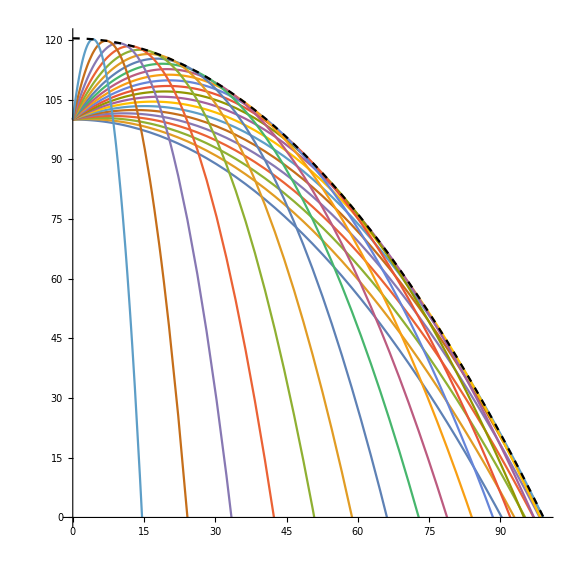

```mathematica
CurveBundle=Table[Solve[f[x,y,θ]==0,y][[1,1,2]],{θ,0,(2π)/4-(2π)/90,(2π)/90}];
xmax=Solve[Y==0,x][[2,1,2]];g=981/100;v0=20;y0=100;
Show[
Plot[CurveBundle,{x,0,xmax},PlotRange->{0,(Y/.x->0)},AspectRatio->1,ImageSize->Large],
Plot[Y,{x,0,xmax},PlotStyle->Directive[Dashed,Black]]
]
Clear["g","v0","y0"]
```